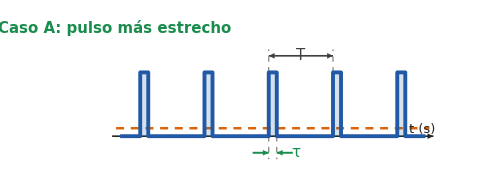
Dominio del tiempo | Dominio de la frecuencia
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* ================================================================== *)
(*  DIAGRAMA: DUALIDAD TIEMPO-FRECUENCIA                               *)
(*  Fila 1: original  |  Fila 2: Caso A (τ menor)  |  Fila 3: Caso B  *)
(* ================================================================== *)

ClearAll[txt, cota, guia, panelTiempo, panelFrecuencia];

(* ---------- Datos y rangos mostrados ---------- *)
amp  = 5;          (* V : amplitud *)
tMax = 20;         (* el tiempo se muestra en [-tMax, tMax] *)
wMax = 4 Pi;       (* el espectro se muestra en [-wMax, wMax] *)

(* ---------- Estilo ---------- *)
colSenal   = RGBColor[0.13, 0.35, 0.65];
colRelleno = RGBColor[0.13, 0.35, 0.65, 0.18];
colDC      = RGBColor[0.85, 0.40, 0.05];     (* continua / valor medio *)
colResto   = GrayLevel[0.70];                (* lóbulos laterales *)
colCero    = RGBColor[0.75, 0.10, 0.10];     (* cortes por cero *)
colLobulo  = RGBColor[0.98, 0.85, 0.35, 0.30];
colCota    = GrayLevel[0.25];
colEje     = GrayLevel[0.15];
colCambio  = RGBColor[0.10, 0.55, 0.30];     (* parámetro que se modifica *)

txt[s_, pos_, off_: {0, 0}, col_: GrayLevel[0.15], sz_: 13] :=
  Text[Style[s, sz, col], pos, off];

cota[p1_, p2_, col_: colCota] := {col, AbsoluteThickness[1.2],
   Arrowheads[{-0.018, 0.018}], Arrow[{p1, p2}]};

guia[p1_, p2_] := {GrayLevel[0.45], AbsoluteThickness[0.8],
   Dashing[{0.008, 0.008}], Line[{p1, p2}]};

(* ================================================================== *)
(*  PANEL DE TIEMPO                                                    *)
(* ================================================================== *)
panelTiempo[tau_, per_, titulo_, colTitulo_, cTau_, cPer_] :=
 Module[{k, centros, pulso, senal, nivel},
  k = Floor[16/per];
  centros = Table[j per, {j, -k, k}];
  pulso[c_] := {{c - tau/2, 0}, {c - tau/2, amp}, {c + tau/2, amp}, {c + tau/2, 0}};
  senal = Join[{{-tMax + 1, 0}}, Join @@ (pulso /@ centros), {{tMax - 1, 0}}];
  nivel = amp tau/per;

  Graphics[{
    (* eje del tiempo *)
    {colEje, AbsoluteThickness[1.2], Arrowheads[0.025],
     Arrow[{{-tMax, 0}, {tMax, 0}}]},
    txt["t (s)", {tMax + 0.3, 0}, {1, -1.6}],

    (* valor medio (componente continua) *)
    {colDC, AbsoluteThickness[1.8], Dashing[{0.012, 0.01}],
     Line[{{-tMax + 0.5, nivel}, {tMax - 0.5, nivel}}]},

    (* pulsos *)
    {colRelleno, EdgeForm[None], Polygon[pulso[#]] & /@ centros},
    {colSenal, AbsoluteThickness[2.8], Line[senal]},

    (* cota de la anchura del pulso (flechas hacia dentro) *)
    guia[{-tau/2, 0}, {-tau/2, -1.8}], guia[{tau/2, 0}, {tau/2, -1.8}],
    {cTau, AbsoluteThickness[1.4], Arrowheads[0.02],
     Arrow[{{-tau/2 - 2, -1.3}, {-tau/2, -1.3}}],
     Arrow[{{tau/2 + 2, -1.3}, {tau/2, -1.3}}]},
    txt["τ", {tau/2 + 2.4, -1.3}, {-1, 0}, cTau, 15],

    (* cota del período *)
    guia[{-tau/2, amp}, {-tau/2, amp + 1.8}],
    guia[{per - tau/2, amp}, {per - tau/2, amp + 1.8}],
    cota[{-tau/2, amp + 1.3}, {per - tau/2, amp + 1.3}, cPer],
    txt["T", {(per - tau)/2, amp + 1.3}, {0, -1.4}, cPer, 15],

    (* título de la fila *)
    txt[Style[titulo, Bold], {-tMax + 0.3, amp + 3.5}, {-1, 0}, colTitulo, 15]
   },
   PlotRange -> {{-tMax - 0.5, tMax + 0.5}, {-3, 9.3}},
   PlotRangePadding -> 0, AspectRatio -> 0.4, ImageSize -> 480]];

(* ================================================================== *)
(*  PANEL DE FRECUENCIA                                                *)
(*  Altura de cada línea = |c_n|/T  (la continua vale V·τ/T)           *)
(* ================================================================== *)
panelFrecuencia[tau_, per_, conLeyenda_] :=
 Module[{w1, wz, nMax, nivel, alt, env, colN, fino, tallos, curva,
   lobulo, ceros, etiquetas, leyenda},
  w1 = 2 Pi/per;            (* separación entre armónicos *)
  wz = 2 Pi/tau;            (* primer corte por cero *)
  nMax = Floor[wMax/w1];
  nivel = amp tau/per;
  alt[n_] := N[nivel Abs[Sinc[n w1 tau/2]]];
  env[w_] := nivel Abs[Sinc[w tau/2]];
  colN[n_] := Which[n == 0, colDC, Abs[n w1] < wz - 10^-6, colSenal, True, colResto];
  fino = nMax > 20;

  tallos = Table[{colN[n], AbsoluteThickness[If[fino, 1.6, 3]],
     Line[{{n w1, 0}, {n w1, alt[n]}}],
     If[fino, {}, {PointSize[0.012], Point[{n w1, alt[n]}]}]},
    {n, -nMax, nMax}];

  curva  = Table[{w, env[w]}, {w, -N[wMax], N[wMax], 0.02}];
  lobulo = Polygon[Join[{{-wz, 0}},
     Table[{w, env[w]}, {w, -N[wz], N[wz], 0.02}], {{wz, 0}}]];
  ceros  = Table[{k wz, 0},
     {k, DeleteCases[Range[-Floor[wMax/wz], Floor[wMax/wz]], 0]}];
  etiquetas = {"−4π", "−3π", "−2π", "−π", "0", "π", "2π", "3π", "4π"};

  (* leyenda (solo en el primer panel) *)
  leyenda = If[conLeyenda,
    {EdgeForm[GrayLevel[0.8]], FaceForm[White],
     Rectangle[{4.7, 0.68}, {14.1, 1.9}],
     {colDC, AbsoluteThickness[3], Line[{{5.3, 1.64}, {5.3, 1.80}}]},
     txt["Continua", {6.2, 1.72}, {-1, 0}, GrayLevel[0.15], 12],
     {colSenal, AbsoluteThickness[3], Line[{{5.3, 1.36}, {5.3, 1.52}}]},
     txt["Lóbulo principal", {6.2, 1.44}, {-1, 0}, GrayLevel[0.15], 12],
     {colResto, AbsoluteThickness[3], Line[{{5.3, 1.08}, {5.3, 1.24}}]},
     txt["Lóbulos laterales", {6.2, 1.16}, {-1, 0}, GrayLevel[0.15], 12],
     {colCero, PointSize[0.014], Point[{5.3, 0.88}]},
     txt["Cortes por cero", {6.2, 0.88}, {-1, 0}, GrayLevel[0.15], 12]},
    {}];

  Graphics[{
    (* lóbulo principal sombreado y envolvente *)
    {colLobulo, EdgeForm[None], lobulo},
    {GrayLevel[0.3], AbsoluteThickness[1.5], Dashing[{0.01, 0.008}], Line[curva]},

    (* líneas espectrales *)
    tallos,

    (* guías, marcas de cortes por cero y cota del lóbulo *)
    {colCero, AbsoluteThickness[1], Dashing[{0.008, 0.008}],
     Line[{{-wz, 0}, {-wz, 1.5}}], Line[{{wz, 0}, {wz, 1.5}}]},
    {colCero, PointSize[0.016], Point[ceros]},
    cota[{-wz, 1.5}, {wz, 1.5}],
    txt["Lóbulo principal", {0, 1.5}, {0, -1.4}, GrayLevel[0.15], 12],

    (* ejes *)
    {colEje, AbsoluteThickness[1.2], Arrowheads[0.02],
     Arrow[{{-4.4 Pi, 0}, {4.4 Pi, 0}}],
     Arrow[{{-4.4 Pi, 0}, {-4.4 Pi, 1.45}}]},
    {colEje, AbsoluteThickness[0.8],
     Table[Line[{{k Pi, 0}, {k Pi, -0.04}}], {k, -4, 4}]},
    Table[txt[etiquetas[[k + 5]], {k Pi, -0.05}, {0, 1.3}], {k, -4, 4}],
    txt["ω", {4.4 Pi + 0.3, 0}, {-1, 0}, colEje, 15],

    leyenda
   },
   PlotRange -> {{-4.7 Pi, 4.9 Pi}, {-0.45, 1.95}},
   PlotRangePadding -> 0, AspectRatio -> 0.4, ImageSize -> 480]];

(* ================================================================== *)
(*  FIGURA FINAL                                                       *)
(*  panelTiempo[τ, T, título, colTítulo, colτ, colT]                   *)
(*  panelFrecuencia[τ, T, ¿leyenda?]                                   *)
(* ================================================================== *)
figura = Grid[{
    {Style["Dominio del tiempo", Bold, 17],
     Style["Dominio de la frecuencia", Bold, 17]},
    {panelTiempo[2, 8, "Señal original", colEje, colCota, colCota],
     panelFrecuencia[2, 8, True]},
    {panelTiempo[1, 8, "Caso A: pulso más estrecho", colCambio, colCambio, colCota],
     panelFrecuencia[1, 8, False]},
    {panelTiempo[2, 16, "Caso B: período mayor", colCambio, colCota, colCambio],
     panelFrecuencia[2, 16, False]}},
   Alignment -> Center, Spacings -> {2, 1},
   Dividers -> {False, {False, False, GrayLevel[0.8], GrayLevel[0.8], False}}]

(* Exportación (PDF vectorial recomendado para \includegraphics en LaTeX) *)
(* Export["diagrama_dualidad.pdf", figura];
   Export["diagrama_dualidad.png", figura, ImageResolution -> 300]; *)
```

```mathematica
Export[CloudObject["T2_pulso_rectangular_P2_a.png"], figura, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800];
```